0.0214155-2.01456 x

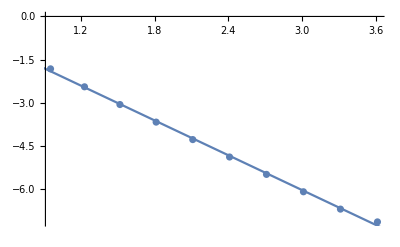

```mathematica
output=
{
{9,0.0152549916716770},{17,0.0036350128595307},{33,0.0008822534716679},{65,0.0002169073938631},{129,0.0000537448264770},{257,0.0000133742590753},{513,0.0000033357109875},{1025,0.0000008329452357},{2049,0.0000002084629935},{4097,0.0000000751291005}
};
f=Normal@LinearModelFit[Log10@output⟦1;;-1⟧,{x},x]
Show[ListPlot@Log10@output,Plot[f,{x,0,4}]]
```

```mathematica
E^7.
```

1096.63

```mathematica
{8,0.0002346446549774},{16,0.0000107755524099},{32,0.0000005743324006},{64,0.0000000649786230},{128,0.0000000410900667},{256,0.0000000290899905},{512,0.0000000205784033},{1024,0.0000000147364712},
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Chengzhe\Desktop\LIS2T\20181128_Zhou_Troian_JFMRapids_DynamicTaylorCone\Code\spline\Output

{{0,0.19635,0},{0.0980171,0.195404,-0.00377886},{0.19509,0.192577,-0.00752136},{0.290285,0.187895,-0.0111914},{0.382683,0.181403,-0.0147537},{0.471397,0.173165,-0.0181738},{0.55557,0.163259,-0.021419},{0.634393,0.15178,-0.0244578},{0.707107,0.13884,-0.0272612},{0.77301,0.124563,-0.0298019},{0.83147,0.109086,-0.0320558},{0.881921,0.0925585,-0.0340008},{0.92388,0.0751397,-0.0356185},{0.95694,0.0569973,-0.036893},{0.980785,0.0383059,-0.0378124},{0.995185,0.0192456,-0.0383674},{1,-1.11814×10^-16,-0.0385532},{0.995185,-0.0192456,-0.0383674},{0.980785,-0.0383059,-0.0378124},{0.95694,-0.0569973,-0.036893},{0.92388,-0.0751397,-0.0356185},{0.881921,-0.0925585,-0.0340008},{0.83147,-0.109086,-0.0320558},{0.77301,-0.124563,-0.0298019},{0.707107,-0.13884,-0.0272612},{0.634393,-0.15178,-0.0244578},{0.55557,-0.163259,-0.021419},{0.471397,-0.173165,-0.0181738},{0.382683,-0.181403,-0.0147537},{0.290285,-0.187895,-0.0111914},{0.19509,-0.192577,-0.00752136},{0.0980171,-0.195404,-0.00377886},{2.39392×10^-16,-0.19635,2.0331×10^-15},{1,-1.98254×10^-18,-0.0385532},{0.995185,-0.0192456,-0.0383674},{0.980785,-0.0383059,-0.0378124},{0.95694,-0.0569973,-0.036893},{0.92388,-0.0751397,-0.0356185},{0.881921,-0.0925585,-0.0340008},{0.83147,-0.109086,-0.0320558},{0.77301,-0.124563,-0.0298019},{0.707107,-0.13884,-0.0272612},{0.634393,-0.15178,-0.0244578},{0.55557,-0.163259,-0.021419},{0.471397,-0.173165,-0.0181738},{0.382683,-0.181403,-0.0147537},{0.290285,-0.187895,-0.0111914},{0.19509,-0.192577,-0.00752136},{0.0980171,-0.195404,-0.00377886},{6.12323×10^-17,-0.19635,-2.57793×10^-17},{-0.0980171,-0.195404,0.00377886},{-0.19509,-0.192577,0.00752136},{-0.290285,-0.187895,0.0111914},{-0.382683,-0.181403,0.0147537},{-0.471397,-0.173165,0.0181738},{-0.55557,-0.163259,0.021419},{-0.634393,-0.15178,0.0244578},{-0.707107,-0.13884,0.0272612},{-0.77301,-0.124563,0.0298019},{-0.83147,-0.109086,0.0320558},{-0.881921,-0.0925585,0.0340008},{-0.92388,-0.0751397,0.0356185},{-0.95694,-0.0569973,0.036893},{-0.980785,-0.0383059,0.0378124},{-0.995185,-0.0192456,0.0383674},{-1,-2.84495×10^-16,0.0385532}}

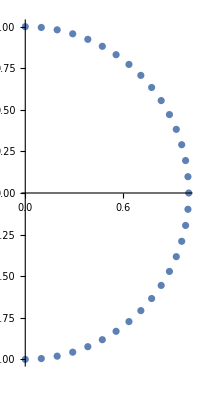

```mathematica
data=Import["tt.txt","Data"]
r=data⟦1;;Length@data/2⟧;
z=data⟦Length@data/2+1;;-1⟧;
ListPlot[Transpose@{r⟦All,1⟧,z⟦All,1⟧},AspectRatio->Automatic]
```